# SciCos - Introduction to Mathematica

Oxford, 11/06/2018

## Introduction

I am not an expert! I am a user!

Mathematica can be used for:

Symbolic computations (probably the best tool)

Numeric computations (be careful, so simple that can hide problems)

Some general property of Mathematica:

Very general (built-in commands for many things)

Easy to use (autocompletion, quick to write down what you want, intuitive)

Customizable (many options for each command)

Slow compared to other programming languages

Dangerous (not precise results if you don’t know what you are doing)

You can not always write your expressions in the form you want them to be

When Mathematica should not be used:

If you want speed

If your problem is complicated and you want to control the different steps

How to get help:

Help -> Wolfram Documentation -> (digit a keyword or navigate)

Type ? before a command

Google (online documentation and forums)

## Variables, Rules and Commands

Blue if your object has no definition stored

```mathematica
var
```

var

Black if there is a definition in Mathematica

```mathematica
var=5
```

5

```mathematica
var
```

5

```mathematica
(a+b)^5
```

(a+b)^5

Expand any expression (% refers to the previous output)

```mathematica
Expand[%]
```

a^5+5 a^4 b+10 a^3 b^2+10 a^2 b^3+5 a b^4+b^5

Tries to factorize an expression

```mathematica
Factor[%]
```

(a+b)^5

Tries to simplify an expression (write it down in the shortest form possible) - Have a look at FullSimplify

```mathematica
Simplify[%%]
```

(a+b)^5

## Manipulation of expressions

Suggestion: use always expressions rather than equations

```mathematica
eq=a+b==5
```

a+b==5

vs

```mathematica
eq=a+b-5
```

-5+a+b

Options:

```mathematica
eq=Sqrt[a^2]
```

√(a^2)

```mathematica
eq // Simplify
```

√(a^2)

```mathematica
Simplify[eq,a>0]
```

a

```mathematica
Simplify[eq,Element[a,Reals]]
```

Abs[a]

## Differential equations

Simple ODE

```mathematica
eq=y''[x]+a y'[x]+b y[x]
```

b y[x]+a y'[x]+y''[x]

Boundary conditions

```mathematica
y0=1
yp0=1/3
```

1

1/3

### DSolve

```mathematica
?DSolve
```

DSolve[eqn,u,x] solves a differential equation for the function u, with independent variable x. 
DSolve[eqn,u,{x,x_min,x_max}] solves a differential equation for x between x_min and x_max.
DSolve[{eqn_1,eqn_2,…},{u_1,u_2,…},…] solves a list of differential equations. 
DSolve[eqn,u,{x_1,x_2,…}] solves a partial differential equation. 
DSolve[eqn,u,{x_1,x_2,…}∈Ω] solves the partial differential equation eqn over the region Ω.

If we don’t specify boundary conditions the result is given in terms of C[i]

```mathematica
eq
```

b y[x]+a y'[x]+y''[x]

```mathematica
sol=DSolve[{eq==0},y,x]
```

{{y→Function[{x},ⅇ^(1/2 (-a-√(a^2-4 b)) x) C[1]+ⅇ^(1/2 (-a+√(a^2-4 b)) x) C[2]]}}

```mathematica
sol=DSolve[{eq==0,y[0]==y0,y'[0]==yp0},y,x]
```

{{y→Function[{x},1/(6 √(a^2-4 b))(-2 ⅇ^(1/2 (-a-√(a^2-4 b)) x)-3 a ⅇ^(1/2 (-a-√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a-√(a^2-4 b)) x)+2 ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 a ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a+√(a^2-4 b)) x))]}}

Let’s try to plot the solution

```mathematica
sol
Plot[%,{x,0,4}]
```

{{y→Function[{x},1/(6 √(a^2-4 b))(-2 ⅇ^(1/2 (-a-√(a^2-4 b)) x)-3 a ⅇ^(1/2 (-a-√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a-√(a^2-4 b)) x)+2 ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 a ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a+√(a^2-4 b)) x))]}}

-Graphics-

NO! sol is a rule, not a variable

```mathematica
y[x] //.sol
Plot[%,{x,0,4}]
```

{1/(6 √(a^2-4 b))(-2 ⅇ^(1/2 (-a-√(a^2-4 b)) x)-3 a ⅇ^(1/2 (-a-√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a-√(a^2-4 b)) x)+2 ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 a ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a+√(a^2-4 b)) x))}

-Graphics-

NO! Curly brackets are there because in general we can have multiple solutions

```mathematica
Flatten[sol]
```

{y→Function[{x},1/(6 √(a^2-4 b))(-2 ⅇ^(1/2 (-a-√(a^2-4 b)) x)-3 a ⅇ^(1/2 (-a-√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a-√(a^2-4 b)) x)+2 ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 a ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a+√(a^2-4 b)) x))]}

```mathematica
soly = y[x] //.Flatten[sol]
Plot[%,{x,0,4}]
```

1/(6 √(a^2-4 b))(-2 ⅇ^(1/2 (-a-√(a^2-4 b)) x)-3 a ⅇ^(1/2 (-a-√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a-√(a^2-4 b)) x)+2 ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 a ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a+√(a^2-4 b)) x))

-Graphics-

NO! The expression is there, but a and b are unspecified

-1/(6 √151)ⅈ (-11 ⅇ^(1/2 (-3-ⅈ √151) x)+3 ⅈ √151 ⅇ^(1/2 (-3-ⅈ √151) x)+11 ⅇ^(1/2 (-3+ⅈ √151) x)+3 ⅈ √151 ⅇ^(1/2 (-3+ⅈ √151) x))

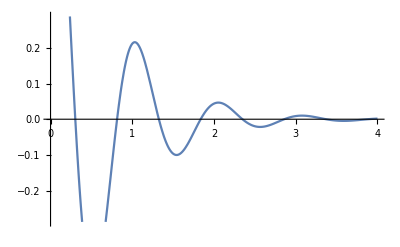

```mathematica
y[x] //.Flatten[sol] //.a->3 //.b->40
Plot[%,{x,0,4}]
```

```mathematica
eq
```

b y[x]+a y'[x]+y''[x]

Better, at least we have a plot! However, if we want a more familiar expression in terms of trigonometric functions..

1/2 Cosh[(3 x)/2-1/2 ⅈ √151 x]-(11 ⅈ Cosh[(3 x)/2-1/2 ⅈ √151 x])/(6 √151)+1/2 Cosh[(3 x)/2+1/2 ⅈ √151 x]+(11 ⅈ Cosh[(3 x)/2+1/2 ⅈ √151 x])/(6 √151)-1/2 Sinh[(3 x)/2-1/2 ⅈ √151 x]+(11 ⅈ Sinh[(3 x)/2-1/2 ⅈ √151 x])/(6 √151)-1/2 Sinh[(3 x)/2+1/2 ⅈ √151 x]-(11 ⅈ Sinh[(3 x)/2+1/2 ⅈ √151 x])/(6 √151)

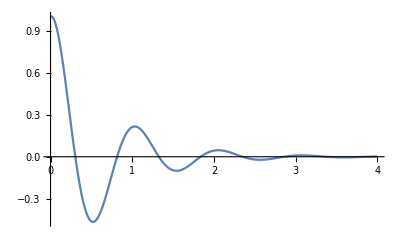

```mathematica
y[x] //.Flatten[sol] //.a->3 //.b->40 // ExpToTrig
Plot[%,{x,0,4},PlotRange->All]
```

Better! But still it can be improved. The solution is real, I don’t want all these complex numbers

```mathematica
y[x] //.Flatten[sol] //.a->3 //.b->40
Re[%]
Im[%]
```

-1/(6 √151)ⅈ (-11 ⅇ^(1/2 (-3-ⅈ √151) x)+3 ⅈ √151 ⅇ^(1/2 (-3-ⅈ √151) x)+11 ⅇ^(1/2 (-3+ⅈ √151) x)+3 ⅈ √151 ⅇ^(1/2 (-3+ⅈ √151) x))

1/(6 √151)(Im[-11 ⅇ^(1/2 (-3-ⅈ √151) x)+11 ⅇ^(1/2 (-3+ⅈ √151) x)]+3 √151 Re[ⅇ^(1/2 (-3-ⅈ √151) x)]+3 √151 Re[ⅇ^(1/2 (-3+ⅈ √151) x)])

0

```mathematica
y[x] //.Flatten[sol] //.a->3 //.b->40 // ExpToTrig // Simplify
Plot[%,{x,0,4},PlotRange->All]
```

1/453 (453 Cos[(√151 x)/2]+11 √151 Sin[(√151 x)/2]) (Cosh[(3 x)/2]-Sinh[(3 x)/2])

-Graphics-

What if I want to plot the solution for different values of a and b?

1/(6 √(a^2-4 b))(-2 ⅇ^(1/2 (-a-√(a^2-4 b)) x)-3 a ⅇ^(1/2 (-a-√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a-√(a^2-4 b)) x)+2 ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 a ⅇ^(1/2 (-a+√(a^2-4 b)) x)+3 √(a^2-4 b) ⅇ^(1/2 (-a+√(a^2-4 b)) x))

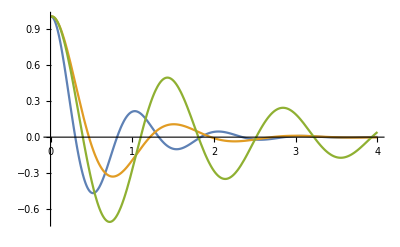

```mathematica
y[x] //.Flatten[sol]
Plot[{% //.a->3 //.b->40, % //.a->3 //.b->20, % //.a->1 //.b->20},{x,0,4},PlotRange->All]
```

### NDSolve

```mathematica
?NDSolve
```

NDSolve[eqns,u,{x,x_min,x_max}] finds a numerical solution to the ordinary differential equations eqns for the function u with the independent variable x in the range x_min to x_max. 
NDSolve[eqns,u,{x,x_min,x_max},{y,y_min,y_max}] solves the partial differential equations eqns over a rectangular region.
NDSolve[eqns,u,{x,y}∈Ω] solves the partial differential equations eqns over the region Ω.
NDSolve[eqns,u,{t,t_min,t_max},{x,y}∈Ω] solves the time-dependent partial differential equations eqns over the region Ω.
NDSolve[eqns,{u_1,u_2,…},…] solves for the functions u_i.

Let’s try to solve the same equation numerically

```mathematica
sol=NDSolve[{eq==0,y[0]==y0,y'[0]==yp0},y,x]
```

NDSolve::ndlim: Range specification x is not of the form {x, xend} or {x, xmin, xmax}.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

NDSolve[{b y[x]+a y'[x]+y''[x]==0,y[0]==1,y'[0]==1/3},y,x]

Errors! We need to specify a range for x

```mathematica
sol=NDSolve[{eq==0,y[0]==y0,y'[0]==yp0},y,{x,0,4}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

NDSolve[{b y[x]+a y'[x]+y''[x]==0,y[0]==1,y'[0]==1/3},y,{x,0,4}]

Error! Non-numerical value! (we didn’t specify a and b)

```mathematica
sol1=Flatten[NDSolve[{eq==0,y[0]==y0,y'[0]==yp0} //.a->3 //.b->40,y,{x,0,4}]]
```

{y→InterpolatingFunction[…]}

OK, now it works! Let’s try to calculate the solution for different values of a and b

```mathematica
sol2=Flatten[NDSolve[{eq==0,y[0]==y0,y'[0]==yp0} //.a->3 //.b->20,y,{x,0,4}]]
```

{y→InterpolatingFunction[…]}

```mathematica
sol3=Flatten[NDSolve[{eq==0,y[0]==y0,y'[0]==yp0} //.a->1 //.b->20,y,{x,0,4}]]
```

{y→InterpolatingFunction[…]}

And now plot it!

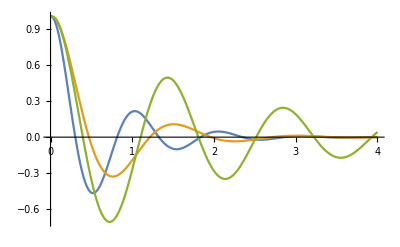

```mathematica
Plot[{y[x] //.sol1,y[x] //.sol2,y[x] //.sol3},{x,0,4},PlotRange->All]
```

Relative difference between the two solutions. This is how to define a new command. Look at the green patterns!

```mathematica
RelDiff[sol1_,sol2_]:=Abs[sol1/sol2-1]
```

Let’s see if it works as expected

```mathematica
RelDiff[y[x] //.sol1, soly //.a:>3 //.b:>40]
```

Abs[-1+(6 ⅈ √151 InterpolatingFunction[…][x])/(-11 ⅇ^(1/2 (-3-ⅈ √151) x)+3 ⅈ √151 ⅇ^(1/2 (-3-ⅈ √151) x)+11 ⅇ^(1/2 (-3+ⅈ √151) x)+3 ⅈ √151 ⅇ^(1/2 (-3+ⅈ √151) x))]

Plot the relative difference

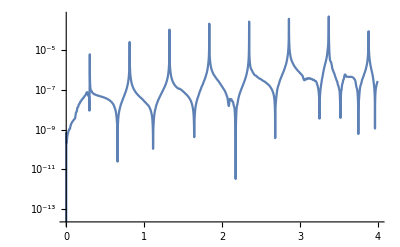

```mathematica
LogPlot[RelDiff[y[x] //.sol1, soly //.a:>3 //.b:>40],{x,0,4},PlotRange->All]
```

Clearly the relative difference is not 0! Spikes are there when the function crosses 0

### ParametricNDSolve

```mathematica
?ParametricNDSolve
```

ParametricNDSolve[eqns,u,{x,x_min,x_max},pars] finds a numerical solution to the ordinary differential equations eqns for the function u with the independent variable x in the range x_min to x_max with parameters pars.
ParametricNDSolve[eqns,u,{x,x_min,x_max},{y,y_min,y_max},pars] solves the partial differential equations eqns over a rectangular region.
ParametricNDSolve[eqns,u,{x,y}∈Ω, pars] solves the partial differential equations eqns over the region Ω.
ParametricNDSolve[eqns,u,{t,t_min,t_max},{x,y}∈Ω, pars] solves the time-dependent partial differential equations eqns over the region Ω.
ParametricNDSolve[eqns,{u_1,u_2,…},…] solves for the functions u_i.

More efficient method to solve a differential equation with parameters

```mathematica
sol=ParametricNDSolve[{eq==0,y[0]==y0,y'[0]==yp0},y,{x,0,4},{a,b}]
```

{y→ParametricFunction[<>]}

How to use it?

```mathematica
y //.sol
```

$Aborted

We had to abort the command. Let’s try this

```mathematica
y[x] //.sol
```

$Aborted

Again! We have to specify the parameters a and b

```mathematica
y[a,b][x] //.sol
```

$Aborted

Again! We have to give them a numerical value!

```mathematica
y[3,40][x] //.sol
```

InterpolatingFunction[…][x]

Bingo! Let’s plot it!

```mathematica
Plot[{y[3,40][x] //.sol,y[3,20][x] //.sol,y[1,20][x] //.sol},{x,0,4},PlotRange->All]
```

-Graphics-

### Problematic Example (no solution given)

Friedmann equation (standard equation in cosmology)

```mathematica
eq=h[a]^2-Omr a^-4-Omm a^-3
```

-Omm/a^3-Omr/a^4+h[a]^2

We start integrating it back in the past

```mathematica
aini=10^-14
```

1/100000000000000

Some rules, the second one is to have h=1 today

```mathematica
rules={Omr->10^-4,Omm->1-Omr}
```

{Omr→1/10000,Omm→1-Omr}

Let’s verify it!

```mathematica
eq //.rules //.a->1
```

-1+h[1]^2

Now, solution for h (as expected 2 solutions)

```mathematica
Solve[eq==0,h[a]]
solh=%[[2]]
```

{{h[a]→-(√(a Omm+Omr))/a^2},{h[a]→(√(a Omm+Omr))/a^2}}

{h[a]→(√(a Omm+Omr))/a^2}

Now plot it!

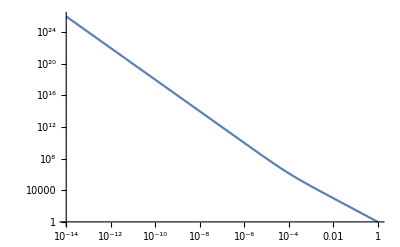

```mathematica
LogLogPlot[h[a] //.solh //.rules,{a,aini,1}]
```

What if we solve numerically the derivative?

```mathematica
eq
```

-Omm/a^3-Omr/a^4+h[a]^2

```mathematica
eqD=D[eq,a]
```

(3 Omm)/a^4+(4 Omr)/a^5+2 h[a] h'[a]

Now we have the analytic derivative, let me plug in the solution for h

```mathematica
eqD=eqD //.solh
```

(3 Omm)/a^4+(4 Omr)/a^5+(2 √(a Omm+Omr) h'[a])/a^2

The system we have to solve is now

```mathematica
{eqD==0,h[aini]==Evaluate[h[a] //.solh //.a->aini]} //.rules
```

{1/(2500 a^5)+29997/(10000 a^4)+(2 √(1/10000+(9999 a)/10000) h'[a])/a^2==0,h[1/100000000000000]==10000000000000000000 √100000000009999}

Now use NDSolve

```mathematica
solhN=Flatten[NDSolve[%,h,{a,aini,1}]]
```

{h→InterpolatingFunction[…]}

Bingo! Now let’s plot it!

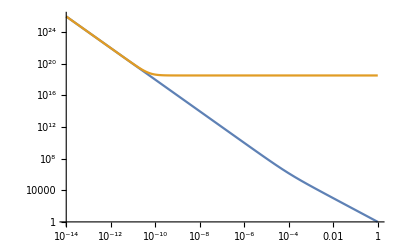

```mathematica
LogLogPlot[{h[a] //.solh //.rules,h[a] //.solhN},{a,aini,1}]
```

What? Do you see the little difference with respect to the analytic solution?

Check possible methods to solve numerically a differential equation

## Integrals

### Integrate

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

Basic integration

```mathematica
int=x^2
```

x^2

Indefinite integral (true result up to a constant)

```mathematica
Integrate[int,x]
```

x^3/3

Definite integral! A number, as expected

```mathematica
Integrate[int,{x,0,2}]
```

8/3

Sometimes complicated results

```mathematica
int=x Sin[x]Cos[x^2]
```

x Cos[x^2] Sin[x]

```mathematica
solint=Integrate[int,x]
```

1/8 (2 Cos[(-1+x) x]-2 Cos[x (1+x)]+√(2 π) (-Cos[1/4] FresnelS[(-1+2 x)/(√(2 π))]+FresnelC[(-1+2 x)/(√(2 π))] Sin[1/4])+√(2 π) (-Cos[1/4] FresnelS[(1+2 x)/(√(2 π))]+FresnelC[(1+2 x)/(√(2 π))] Sin[1/4]))

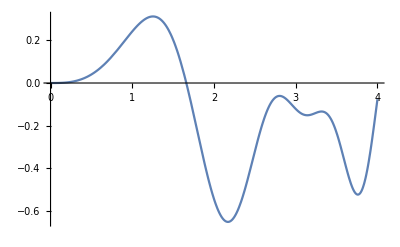

```mathematica
Plot[solint,{x,0,4}]
```

Sometimes not able to integrate

```mathematica
Integrate[x Sin[x]Cos[x^2] Log[x],x]
```

∫x Cos[x^2] Log[x] Sin[x]ⅆx

Not always the desired result (it’s up to you to verify if the solution makes sense)

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[x^-1,x]
```

Log[x]

Sometimes you will find conditional expressions

```mathematica
Integrate[x^n,{x,0,1}]
```

ConditionalExpression[1/(1+n),Re[n]>-1]

Let’s use assumptions

```mathematica
Integrate[x^n,{x,0,1},Assumptions->n>-1]
```

1/(1+n)

### NIntegrate

```mathematica
?NIntegrate
```

NIntegrate[f,{x,x_min,x_max}] gives a numerical approximation to the integral ∫_x_min^x_max f dx. 
NIntegrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives a numerical approximation to the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.
NIntegrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

Now, numerical integration of the complicated integral before

```mathematica
int
```

x Cos[x^2] Sin[x]

```mathematica
NIntegrate[int,{x,0,4}]
```

-0.0759599

Check if the analytic integral gives the same result

```mathematica
solint
```

1/8 (2 Cos[(-1+x) x]-2 Cos[x (1+x)]+√(2 π) (-Cos[1/4] FresnelS[(-1+2 x)/(√(2 π))]+FresnelC[(-1+2 x)/(√(2 π))] Sin[1/4])+√(2 π) (-Cos[1/4] FresnelS[(1+2 x)/(√(2 π))]+FresnelC[(1+2 x)/(√(2 π))] Sin[1/4]))

```mathematica
solint //.x->4 // N
```

-0.0759599

Bingo! Let’s now plot the integral as a function of the upper limit (we need a table to discretize the result)

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

Solution of the numerical integral

```mathematica
solintN=Table[NIntegrate[int,{x,0,xi}],{xi,0,4,0.01}]
```

{0.,3.3333×10^-7,2.66656×10^-6,8.99919×10^-6,0.0000213299,0.0000416562,0.0000719739,0.000114277,0.000170556,0.0002428,0.000332993,0.000443116,0.000575145,0.000731052,0.0009128,0.00112235,0.00136165,0.00163265,0.00193727,0.00227745,0.00265511,0.00307213,0.00353041,0.00403184,0.00457826,0.00517153,0.00581347,0.0065059,0.00725059,0.00804932,0.00890383,0.00981583,0.010787,0.0118191,0.0129136,0.0140722,0.0152964,0.0165878,0.0179478,0.0193779,0.0208795,0.0224539,0.0241024,0.0258263,0.0276268,0.0295049,0.0314618,0.0334985,0.0356158,0.0378147,0.0400959,0.0424601,0.044908,0.0474401,0.0500568,0.0527584,0.0555453,0.0584176,0.0613753,0.0644183,0.0675465,0.0707596,0.0740571,0.0774384,0.080903,0.0844499,0.0880782,0.0917869,0.0955746,0.0994399,0.103381,0.107397,0.111485,0.115644,0.119871,0.124163,0.128519,0.132935,0.137409,0.141937,0.146516,0.151142,0.155812,0.160521,0.165266,0.170043,0.174846,0.17967,0.184512,0.189365,0.194225,0.199085,0.20394,0.208784,0.213611,0.218413,0.223185,0.22792,0.232609,0.237247,0.241826,0.246338,0.250775,0.255129,0.259392,0.263555,0.267611,0.27155,0.275363,0.279042,0.282578,0.285961,0.289182,0.292231,0.295099,0.297778,0.300256,0.302524,0.304573,0.306393,0.307974,0.309307,0.310382,0.31119,0.31172,0.311965,0.311914,0.311559,0.31089,0.309899,0.308578,0.306917,0.30491,0.302548,0.299823,0.29673,0.29326,0.289408,0.285167,0.280532,0.275498,0.270061,0.264215,0.257958,0.251286,0.244198,0.23669,0.228762,0.220413,0.211644,0.202454,0.192846,0.182822,0.172385,0.161537,0.150285,0.138633,0.126587,0.114154,0.101343,0.088161,0.0746186,0.0607259,0.0464941,0.0319355,0.0170631,0.00189069,-0.0135669,-0.0292939,-0.045274,-0.0614897,-0.0779229,-0.0945545,-0.111365,-0.128333,-0.145438,-0.162657,-0.179969,-0.197348,-0.214772,-0.232215,-0.249652,-0.267058,-0.284406,-0.301669,-0.31882,-0.335833,-0.352678,-0.369329,-0.385758,-0.401936,-0.417835,-0.433427,-0.448684,-0.463579,-0.478083,-0.492171,-0.505814,-0.518987,-0.531664,-0.543819,-0.55543,-0.566471,-0.576921,-0.586758,-0.59596,-0.604508,-0.612385,-0.619572,-0.626054,-0.631817,-0.636847,-0.641133,-0.644665,-0.647435,-0.649437,-0.650664,-0.651116,-0.650789,-0.649686,-0.647808,-0.64516,-0.641749,-0.637583,-0.632672,-0.627029,-0.620668,-0.613605,-0.605858,-0.597448,-0.588396,-0.578726,-0.568464,-0.557637,-0.546273,-0.534404,-0.522062,-0.50928,-0.496092,-0.482535,-0.468645,-0.454462,-0.440024,-0.425371,-0.410544,-0.395583,-0.38053,-0.365427,-0.350315,-0.335236,-0.320232,-0.305343,-0.29061,-0.276073,-0.261771,-0.247741,-0.234022,-0.220648,-0.207654,-0.195072,-0.182932,-0.171265,-0.160096,-0.149451,-0.139352,-0.12982,-0.120871,-0.112523,-0.104786,-0.0976716,-0.0911868,-0.0853359,-0.0801209,-0.0755405,-0.071591,-0.0682656,-0.0655551,-0.0634471,-0.061927,-0.0609773,-0.0605781,-0.0607072,-0.0613399,-0.0624496,-0.0640074,-0.0659829,-0.0683437,-0.0710562,-0.0740852,-0.0773946,-0.0809475,-0.0847061,-0.0886324,-0.0926882,-0.0968353,-0.101036,-0.105253,-0.109449,-0.11359,-0.117641,-0.12157,-0.125346,-0.12894,-0.132327,-0.135481,-0.138383,-0.141013,-0.143357,-0.145402,-0.147139,-0.148564,-0.149673,-0.15047,-0.150959,-0.151149,-0.151054,-0.15069,-0.150077,-0.149237,-0.148199,-0.146992,-0.145649,-0.144206,-0.142702,-0.141177,-0.139675,-0.138241,-0.13692,-0.135761,-0.13481,-0.134117,-0.133729,-0.133695,-0.13406,-0.134872,-0.136173,-0.138004,-0.140405,-0.14341,-0.147053,-0.15136,-0.156355,-0.162058,-0.168481,-0.175633,-0.183516,-0.192126,-0.201455,-0.211484,-0.222191,-0.233547,-0.245514,-0.25805,-0.271103,-0.284618,-0.298532,-0.312773,-0.327268,-0.341935,-0.356688,-0.371434,-0.38608,-0.400525,-0.414667,-0.428401,-0.44162,-0.454217,-0.466083,-0.47711,-0.487194,-0.496229,-0.504115,-0.510755,-0.516057,-0.519935,-0.522311,-0.523111,-0.522272,-0.51974,-0.515472,-0.509432,-0.501598,-0.491961,-0.480521,-0.467293,-0.452306,-0.435601,-0.417232,-0.397268,-0.375792,-0.3529,-0.3287,-0.303315,-0.276879,-0.249538,-0.221449,-0.192781,-0.163709,-0.134419,-0.105104,-0.0759599}

Solution of the analytic integral

```mathematica
solint=Table[Integrate[int,{x,0,xi}],{xi,0,4,0.01}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/8 (-√(2 π) (Cos[1/4] FresnelS[Power[«2»]]-FresnelC[Power[«2»]] Sin[1/4])-√(2 π) (-Cos[1/4] FresnelS[Power[«2»]]+FresnelC[Power[«2»]] Sin[1/4]))+1/8 (√(2 π) («1»)+«1» «1»).

{0.,3.3333×10^-7,2.66656×10^-6,8.99919×10^-6,0.0000213299,0.0000416562,0.0000719739,0.000114277,0.000170556,0.0002428,0.000332993,0.000443116,0.000575145,0.000731052,0.0009128,0.00112235,0.00136165,0.00163265,0.00193727,0.00227745,0.00265511,0.00307213,0.00353041,0.00403184,0.00457826,0.00517153,0.00581347,0.0065059,0.00725059,0.00804932,0.00890383,0.00981583,0.010787,0.0118191,0.0129136,0.0140722,0.0152964,0.0165878,0.0179478,0.0193779,0.0208795,0.0224539,0.0241024,0.0258263,0.0276268,0.0295049,0.0314618,0.0334985,0.0356158,0.0378147,0.0400959,0.0424601,0.044908,0.0474401,0.0500568,0.0527584,0.0555453,0.0584176,0.0613753,0.0644183,0.0675465,0.0707596,0.0740571,0.0774384,0.080903,0.0844499,0.0880782,0.0917869,0.0955746,0.0994399,0.103381,0.107397,0.111485,0.115644,0.119871,0.124163,0.128519,0.132935,0.137409,0.141937,0.146516,0.151142,0.155812,0.160521,0.165266,0.170043,0.174846,0.17967,0.184512,0.189365,0.194225,0.199085,0.20394,0.208784,0.213611,0.218413,0.223185,0.22792,0.232609,0.237247,0.241826,0.246338,0.250775,0.255129,0.259392,0.263555,0.267611,0.27155,0.275363,0.279042,0.282578,0.285961,0.289182,0.292231,0.295099,0.297778,0.300256,0.302524,0.304573,0.306393,0.307974,0.309307,0.310382,0.31119,0.31172,0.311965,0.311914,0.311559,0.31089,0.309899,0.308578,0.306917,0.30491,0.302548,0.299823,0.29673,0.29326,0.289408,0.285167,0.280532,0.275498,0.270061,0.264215,0.257958,0.251286,0.244198,0.23669,0.228762,0.220413,0.211644,0.202454,0.192846,0.182822,0.172385,0.161537,0.150285,0.138633,0.126587,0.114154,0.101343,0.088161,0.0746186,0.0607259,0.0464941,0.0319355,0.0170631,0.00189069,-0.0135669,-0.0292939,-0.045274,-0.0614897,-0.0779229,-0.0945545,-0.111365,-0.128333,-0.145438,-0.162657,-0.179969,-0.197348,-0.214772,-0.232215,-0.249652,-0.267058,-0.284406,-0.301669,-0.31882,-0.335833,-0.352678,-0.369329,-0.385758,-0.401936,-0.417835,-0.433427,-0.448684,-0.463579,-0.478083,-0.492171,-0.505814,-0.518987,-0.531664,-0.543819,-0.55543,-0.566471,-0.576921,-0.586758,-0.59596,-0.604508,-0.612385,-0.619572,-0.626054,-0.631817,-0.636847,-0.641133,-0.644665,-0.647435,-0.649437,-0.650664,-0.651116,-0.650789,-0.649686,-0.647808,-0.64516,-0.641749,-0.637583,-0.632672,-0.627029,-0.620668,-0.613605,-0.605858,-0.597448,-0.588396,-0.578726,-0.568464,-0.557637,-0.546273,-0.534404,-0.522062,-0.50928,-0.496092,-0.482535,-0.468645,-0.454462,-0.440024,-0.425371,-0.410544,-0.395583,-0.38053,-0.365427,-0.350315,-0.335236,-0.320232,-0.305343,-0.29061,-0.276073,-0.261771,-0.247741,-0.234022,-0.220648,-0.207654,-0.195072,-0.182932,-0.171265,-0.160096,-0.149451,-0.139352,-0.12982,-0.120871,-0.112523,-0.104786,-0.0976716,-0.0911868,-0.0853359,-0.0801209,-0.0755405,-0.071591,-0.0682656,-0.0655551,-0.0634471,-0.061927,-0.0609773,-0.0605781,-0.0607072,-0.0613399,-0.0624496,-0.0640074,-0.0659829,-0.0683437,-0.0710562,-0.0740852,-0.0773946,-0.0809475,-0.0847061,-0.0886324,-0.0926882,-0.0968353,-0.101036,-0.105253,-0.109449,-0.11359,-0.117641,-0.12157,-0.125346,-0.12894,-0.132327,-0.135481,-0.138383,-0.141013,-0.143357,-0.145402,-0.147139,-0.148564,-0.149673,-0.15047,-0.150959,-0.151149,-0.151054,-0.15069,-0.150077,-0.149237,-0.148199,-0.146992,-0.145649,-0.144206,-0.142702,-0.141177,-0.139675,-0.138241,-0.13692,-0.135761,-0.13481,-0.134117,-0.133729,-0.133695,-0.13406,-0.134872,-0.136173,-0.138004,-0.140405,-0.14341,-0.147053,-0.15136,-0.156355,-0.162058,-0.168481,-0.175633,-0.183516,-0.192126,-0.201455,-0.211484,-0.222191,-0.233547,-0.245514,-0.25805,-0.271103,-0.284618,-0.298532,-0.312773,-0.327268,-0.341935,-0.356688,-0.371434,-0.38608,-0.400525,-0.414667,-0.428401,-0.44162,-0.454217,-0.466083,-0.47711,-0.487194,-0.496229,-0.504115,-0.510755,-0.516057,-0.519935,-0.522311,-0.523111,-0.522272,-0.51974,-0.515472,-0.509432,-0.501598,-0.491961,-0.480521,-0.467293,-0.452306,-0.435601,-0.417232,-0.397268,-0.375792,-0.3529,-0.3287,-0.303315,-0.276879,-0.249538,-0.221449,-0.192781,-0.163709,-0.134419,-0.105104,-0.0759599}

OK! Slower than numerical integral but we still have a result. Read the warning messages! Here we have some precision issue!

Let’s now compare the two results

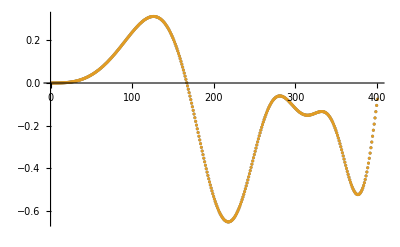

```mathematica
ListPlot[{solintN,solintN}]
```